## Rob’s analysis

```mathematica
Subscript[σ, x]=;
Subscript[σ, y]=;
Subscript[σ, z]=;
```

```mathematica
λ[k_,σ_]:=k/(2*σ);
α[σ_,k_]:=1/2*(Exp[-2*λ[k,σ]^2]-1+Sqrt[2*Pi]*λ[k,σ]*Erf[Sqrt[2]*λ[k,σ]]);
g12[k_,σ_,h_,ϕ_]:=Product[i^2,{i,k}]+h/2*Product[i,{i,α[σ,k]*4*σ^2}]-h/2*Product[i,{i,α[σ,k]*4*σ^2}]*Cos[ϕ];
Ev[k_,σ_,h_]:=h*Product[i,{i,α[σ,k]}]/(h*Product[i,{i,α[σ,k]}]+2*Product[i,{i,λ[k,σ]^2}]);
r[k_,σ_,h_,ϕ_]:=h/2*Product[i,{i,α[σ,k]*σ}]/Product[i^2,{i,λ[k,σ]}];
```

```mathematica
g12[{0.052,0.53,0.47}*10^6,{0.034,0.3,0.3}*10^6,27,Pi/2]/Product[i^2,{i,{0.052,0.53,0.47}*10^6}]
Ev[{0.063,0.063,0.063}*10^6,{0.138,0.132,0.158}*10^6,9]
r[{0.052,0.53,0.47}*10^6,{0.034,0.3,0.3}*10^6*6,3,Pi/2]
α[{0.138,0.132,0.158}*10^6,{0.063,0.063,0.063}*10^6]
λ[{0.063,0.063,0.063}*10^6,{0.138,0.132,0.158}*10^6]
Product[i^2,{i,λ[{0.052,0.53,0.47}*10^6,{0.034,0.3,0.3}*10^6]}]
```

8.64049

0.810776

9.73518×10^17

{0.0512166,0.0558904,0.0392289}

{0.228261,0.238636,0.199367}

0.279983

```mathematica
(4.352847843498329-1)/(4.352847843498329+1)
```

0.626367

```mathematica
+1)
```

{124.331,124.331,124.331}

0.279983

```mathematica
Product[i^2,{i,{0.052,0.53,0.47}*10^6}]
3/2*Product[i,{i,α[{0.063,0.063,0.063}*10^1*4,{0.0063,0.0063,0.0063}*10^6]*{0.063,0.063,0.063}*10^1*4}]
```

1.67785×10^32

7.37695×10^11

```mathematica
62.12389111404524/28
```

2.21871

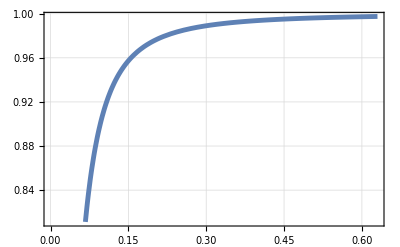

```mathematica
Plot[Product[i,{i,λ[{0.063,0.063,0.063}*10^6,{σ,σ,σ}*10^6]^(-2)*α[{σ,σ,σ}*10^6,{0.063,0.063,0.063}*10^6]}],{σ,0,0.063*10}]
```